## Logic functions

```mathematica
Rule30[parents_List]:=Module[{ruleIndex,ruleBinary},
ruleIndex=parents[[1]]*4+parents[[2]]*2+parents[[3]];
ruleBinary=IntegerDigits[30,2,8];
ruleBinary[[8-ruleIndex]]
];
```

```mathematica
UpdateGeneration[space_List]:=Module[{newSpace},
newSpace=Table[0,{i,1,Length[space]+2}];
left=0;
center=0;
right=space[[1]];

Do[
newSpace[[i]]=Rule30[{left, center, right}];
left = center;
center=right;
right=If[i + 1 <= Length[space],space[[i+1]], 0];
,{i,1,Length[newSpace]}
];
newSpace
];
```

## Read and write functions

```mathematica
ReadGeneration[name_String]:=Module[{binaryData,binaryStrings,fullString,list},
SetDirectory[NotebookDirectory[]];
binaryData=Import["resources/"<>name<>".bin","Byte"];
binaryStrings=IntegerString[#,2,8]&/@binaryData;

binaryStrings=StringReverse/@binaryStrings;
fullString=StringJoin[binaryStrings];
fullString=StringReverse[StringTrim[StringReverse[fullString],StartOfString~~"0"..]];
list=Characters[fullString];
list
]
```

```mathematica
SaveGenerationFromBinaryNumbers[list_List]:=Module[{binaryStrings,binaryData,fileName},(*Asegurarse de que cada elemento de la lista sea un número binario (0 o 1)*)If[!AllTrue[list,(IntegerQ[#]&&#∈{0,1})&],Print["La lista debe contener solo números binarios (0 o 1)."];
Return[]];
(*Agrupar los elementos en bloques de 8 bits*)binaryStrings=StringJoin[ToString[#]&/@#]&/@Partition[list,8];
(*Convertir cada bloque binario en un número entero (byte)*)binaryData=ToExpression["0b"<>#&/@binaryStrings];
(*Generar el nombre del archivo basado en la longitud de la lista*)fileName=ToString[(Length[list]+1)/2];
(*Guardar los datos binarios en un archivo con el nombre generado*)Export["resources/"<>fileName<>".bin",binaryData,"Byte"]]
```

```mathematica
generation=ReadGeneration["5"];
Print[generation];
generation=Update[generation];
Print[generation];
a=SaveGenerationFromBinaryNumbers[generation]
```

{1,1,0,0,1,0,0,0,1}

Update::sym: Argument {1,1,0,0,1,0,0,0,1} at position 1 is expected to be a symbol.

Update[{1,1,0,0,1,0,0,0,1}]

SaveGenerationFromBinaryNumbers[Update[{1,1,0,0,1,0,0,0,1}]]

```mathematica
Print[ReadGeneration["13"]];
```

{}

```mathematica
generation={1};
increment=10;
```

```mathematica
generation=UpdateGeneration[generation];
Do[
Print[generation];
generation=UpdateGeneration[generation];
,{i,0,increment}]
Print[generation]
```

{1,1,1}

{1,1,0,0,1}

{1,1,0,1,1,1,1}

{1,1,0,0,1,0,0,0,1}

{1,1,0,1,1,1,1,0,1,1,1}

{1,1,0,0,1,0,0,0,0,1,0,0,1}

{1,1,0,1,1,1,1,0,0,1,1,1,1,1,1}

{1,1,0,0,1,0,0,0,1,1,1,0,0,0,0,0,1}

{1,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1}

{1,1,0,0,1,0,0,0,0,1,0,1,1,1,1,0,1,1,0,0,1}

{1,1,0,1,1,1,1,0,0,1,1,0,1,0,0,0,0,1,0,1,1,1,1}

{1,1,0,0,1,0,0,0,1,1,1,0,0,1,1,0,0,1,1,0,1,0,0,0,1}

```mathematica
Length[generation]
SaveGenerationFromBinaryNumbers[generation]
```

25

resources/13.bin

## Attractors

Load data

```mathematica
SetDirectory[NotebookDirectory[]];
dataset=Import["./data/attractors.csv","CSV"];

tables=List[];
table=List[];

Do[
If[Length[dataset[[i]]]==3,
AppendTo[table,dataset[[i]]],
AppendTo[tables, table];
table=List[]]
,{i,2,Length[dataset]}];

Clear[table];
```

```mathematica
ZeroProportion=Function[table,
max=StringLength[ToString[Max[table[[;;,1]]]]];
zeros=(Length[table]/((2^max)^2));
Length[table]/(2^max)^2
];
```

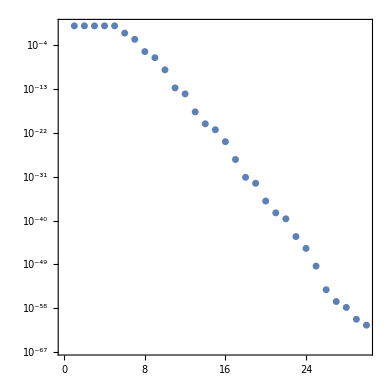

```mathematica
numberOfTransitions=List[];
Do[
AppendTo[numberOfTransitions,ZeroProportion[tables[[i]]]];
,{i,1,Length[tables]}]
ListPlot[numberOfTransitions,ScalingFunctions->"Log",Frame->True,AspectRatio->1]
```

```mathematica
vectorSize=96469;

primes=Join[{1},Prime[Range[vectorSize]]];
subVectors=2500000/primes//IntegerPart;

dots=Transpose[{primes,subVectors}];

p1=First[dots];
p2=Last[dots];

equationGeneral[x_,y_]:=x (p2[[2]]-p1[[2]])+y (p1[[1]]-p2[[1]])+(p2[[1]] p1[[2]]-p1[[1]] p2[[2]]);

distances=Table[(Abs[equationGeneral[dots[[i,1]],dots[[i,2]]]])/(Sqrt[dots[[i,1]]^2+dots[[i,2]]^2]),{i,1,vectorSize}];

index=Position[distances,Max[distances]][[1,1]];

dots[[index]]
```

{1579,1583}

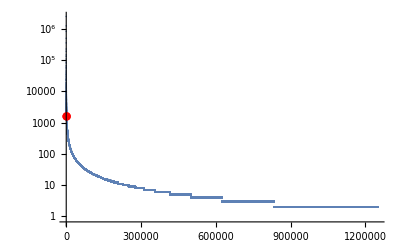

{1579,1583} 13297

{1583,1579}

```mathematica
allDots=ListPlot[dots,PlotRange->All,ScalingFunctions->"Log"];
farestDot=ListPlot[{dots[[index]]},PlotStyle->{Red,PointSize->0.015},ScalingFunctions->"Log"];
Show[allDots,farestDot]
Print[dots[[index]]," ",Prime[primes[[index]]]];
2500000/dots[[index]]//IntegerPart
```